### Start choosing the example:

```mathematica
t=3;
beta=0;
A=0.2;
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"] = {{1,2,3,S1},{3,2,1,S2}};
```

```mathematica
Data
```

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{2,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->800,U1->15,S1->S1,S2->0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: After NewReduce, the system is:
Reduce[S1,ℝ]≥Reduce[0,ℝ]
and the rules are:
<|j517→800,u534→15,j514→800,j515→800,j516→800,j518→0,j519→0,j520→0,j521→0,jt522→0,jt523→800,jt524→800,jt525→0,jt526→800,jt527→0,u530→15,u532→-800+(1615+S1),u533→-800+815,u535→1615+S1,u528→1615+S1,u529→815,u531→1615+S1|>

DataToEquations: It took 0.000556 seconds to reduce with NewReduce!

DataToEquations: Possible multiple solutions 
{Reduce[S1,ℝ]≥Reduce[0,ℝ],<|j517→800,u534→15,j514→800,j515→800,j516→800,j518→0,j519→0,j520→0,j521→0,jt522→0,jt523→800,jt524→800,jt525→0,jt526→800,jt527→0,u530→15,u532→-800+(1615+S1),u533→-800+815,u535→1615+S1,u528→1615+S1,u529→815,u531→1615+S1|>}

DataToEquations: Something went wrong, check the data.

DataToEquations: Done.

{0.013534,Null}

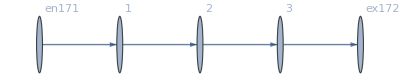

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j514→800,j515→800,j516→800,j517→800,j518→0,j519→0,j520→0,j521→0,jt522→0,jt523→800,jt524→800,jt525→0,jt526→800,jt527→0,u528→1615+S1,u529→815,u530→15,u531→1615+S1,u532→815+S1,u533→15,u534→15,u535→1615+S1|>

```mathematica
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]
```

<|{1,1->2}→1615+S1,{2,2->3}→815,{3,3->ex513}→15,{en512,en512->1}→1615+S1,{2,1->2}→815+S1,{3,2->3}→15,{ex513,3->ex513}→15,{1,en512->1}→1615+S1|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→20.1639,u188→17.582,u189→15.,u190→20.1639,u191→17.582,u192→15.,u193→15.,u194→20.1639|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→21.3227,u188→18.1613,u189→15.,u190→21.3227,u191→18.1613,u192→15.,u193→15.,u194→21.3227|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→25.0478,u188→20.0239,u189→15.,u190→25.0478,u191→20.0239,u192→15.,u193→15.,u194→25.0478|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.20583×10^-13,ComplexInfinity]

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→175.,u188→95.,u189→15.,u190→175.,u191→95.,u192→15.,u193→15.,u194→175.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→742.811,u188→378.906,u189→15.,u190→742.811,u191→378.906,u192→15.,u193→15.,u194→742.811|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→580101.,u188→290058.,u189→15.,u190→580101.,u191→290058.,u192→15.,u193→15.,u194→580101.|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→3.119×10^7,u188→1.5595×10^7,u189→15.,u190→3.119×10^7,u191→1.5595×10^7,u192→15.,u193→15.,u194→3.119×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→4.81052×10^10,u188→2.40526×10^10,u189→15.,u190→4.81052×10^10,u191→2.40526×10^10,u192→15.,u193→15.,u194→4.81052×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→1.12074×10^19,u188→5.6037×10^18,u189→15.,u190→1.12074×10^19,u191→5.6037×10^18,u192→15.,u193→15.,u194→1.12074×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→4.4098×10^106,u188→2.2049×10^106,u189→15.,u190→4.4098×10^106,u191→2.2049×10^106,u192→15.,u193→15.,u194→4.4098×10^106|>